```mathematica
SetDirectory[NotebookDirectory[]];
counts= Drop[Flatten[Import["betaspektrum.TKA", "Table"]], 2][[1;;250]];
energies = Table[-2.14 + 0.353*c, {c, 1, 250}];
data = Transpose[{energies, counts}];
```

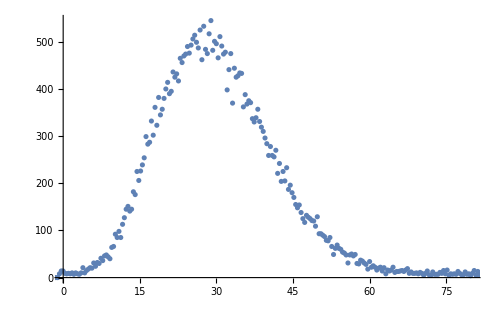

```mathematica
ListPlot[data, PlotRange->{{0, 80}, All}, ImageSize->500]
```

```mathematica
kurie = {#[[1]], √((#[[2]])/(#[[1]])^2)}&/@data;
```

| Estimate | Standard Error | t-Statistic | P-Value
a | -0.0300205 | 0.000358199 | -83.8095 | 2.46616×10^-66
b | 54.2884 | 0.26018 | 208.658 | 3.43517×10^-91

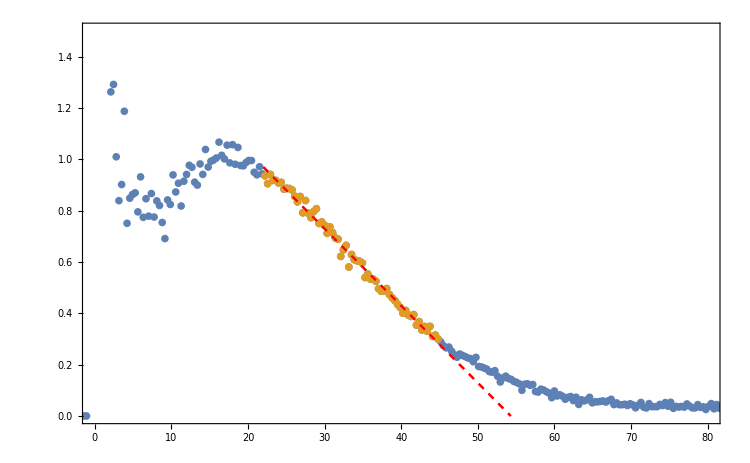

```mathematica
{xmin, xmax} = {22, 45};
fitdata = Select[kurie, #[[1]]>xmin && #[[1]]< xmax&];
nlm = NonlinearModelFit[fitdata, a(x-b), {a, b}, x];
nlm["ParameterTable"]
p = Plot[Normal[nlm], {x, xmin, 60}, Frame->True, ImageSize->750, PlotRange->{{0, 80}, {0, 1.5}}, PlotStyle->{Red, Dashed}];
Show[p, ListPlot[{kurie, fitdata}], p]
```

```mathematica
{m, sm }= nlm["ParameterTableEntries"][[2, {1, 2}]] * 2
massmyon = 105.658
```

{108.577,0.520359}

105.658